```mathematica
SetDirectory@NotebookDirectory[];
```

# Generating Function Functions

Functions to obtain the generating function via recursion.  We use addition to represent coalesent states of ancestral lineages. This works because addition is associative and allows simplification of the branch indices as much as possible along the way.   That means we either pass a fully-labelled set {{a},{b},{c}} and obtain the full generating function for branches of type {a+b} and {c}.  If we pass {{1},{1},{1}} we obtain i-Ton labelled branch types, e.g., {2}, {1}. 

The machinery for the recursion ( below ) will provide the generating function for a fully labelled subset, which we examine for a sample of n=2 lineages.  However, the remaining functions are used to simplify and automate analysis of the i-Ton labelled branches and are defined for a sample of n>2 lineages.

## Neutral Coalescent

### Helper Functions

```mathematica
TakeAway::usage = "TakeAway[U,V]  gives the set U, minus elements V. Note that this is not the same as Complement[U,V] if U contains repeated elements. ";
```

```mathematica
TakeAway[U_List, {}] := U;
(*TakeAway[U_List,{{}}]:=If[MemberQ[U,{{}}],TakeAway[U,{{}}],U];*)
TakeAway[U_List, {v_}] := Drop[U, Cases[Position[U, v],{_Integer}]⟦1⟧] /; Complement[{v}, U] == {};
TakeAway[U_List, V_List] := TakeAway[TakeAway[U, Take[V, 1]], Drop[V, 1]] /; Complement[V, U] == {};
TakeAway[U_List, W__List, V_List] := TakeAway[TakeAway[U, W], V];
```

```mathematica
GetVars::usage="GetVars[expr,ψ] lists the configurations of genes in all terms of the form ψ[ω,genes,options], GetVars[{expr,…},ψ] lists all the variables.";
```

```mathematica
GetVars[expr_,GF_]:=Cases[Variables[GF],expr[_]];
```

```mathematica
(*functions to convert the {a+b+c} notation for the i-Ton branch recursion to the {a,b,c} notation for the fully-labelled topology as described in the manuscript*)
 Listify[yl_List]:=Block[{x = yl[[1]]},
If[Length[x]==0,{x},x[[0]]=List;x]
];ConvertNotation[expr_,ω_]:=expr/.ω[x_]:>   ω[Listify[x]];
```

### Recursion

```mathematica
MakeCoalEvents[xl_List]:=Module[
{myTupleRates = Tally[Subsets[Sort[xl],{2}]],
yl},
yl = {#⟦2⟧,Append[TakeAway[xl,#⟦1⟧],List[Total[Flatten[#⟦1⟧]]]]}&/@myTupleRates
];

GFn[ω_,xl_List]:=Module[{coalList = MakeCoalEvents[xl],λ=Binomial[Length[xl],2]},
If[Length[xl]==1,1,
1/(λ+Total[ω[#]&/@xl])*Total[( #⟦1⟧ * GFn[ω,#⟦2⟧])&/@coalList]
]
];
```

## Starlike Approximation

### Recursion

Note that we retain P[i,n] unevaluated as the probability that i out of n lineages escape the sweep. This can help for analysis as well as for simplification steps.  Substituting P-> PknToAlpha will lead to evaluation as a function of alpha, the scaled distance from the sweep center:  α = r/s Log[2ns], where r is the rate of recombination between the neutral and selected site.

```mathematica
Pe[k_,n_,alpha_]:=Module[
{Pesc = 1 - Exp[-alpha]},
Binomial[n,k]*Pesc^k*(1-Pesc)^(n-k);
(*If[k==0,(1 - Sum[P[j,n],{j,1,n}]),
P[k,n]]*)
P[k,n]
];

PknToAlpha[k_,n_]:=Module[
{Pesc = 1 - Exp[-α]},
Binomial[n,k]*Pesc^k(1-Pesc)^(n-k)
];

MakeStarlikeEvents[xl_List,delta_,alpha_]:=Module[
{myTupleRates,n=Length[xl],numTuples,
yl,returnList={}
},
For[k=0,k<n,k++,
myTupleRates = Tally[Subsets[Sort[xl],{n-k}]];
numTuples = Total[#[[2]] &/@myTupleRates];
yl = {delta*Pe[k,n,alpha]*#⟦2⟧/numTuples,
Append[TakeAway[xl,#⟦1⟧],List[Total[Flatten[#⟦1⟧]]]]}&/@myTupleRates;
returnList = Join[returnList,yl];
];
(*for k = n separate to avoid adding empty {} lineage to branch set*)
yl = {{delta*Pe[n,n,alpha]*1,xl}};
returnList = Join[returnList,yl];
returnList = Flatten[returnList,0];
Return[returnList]
]
GFstar[alpha_,ω_,xl_List,dl_List]:=Module[
{coalList = MakeCoalEvents[xl],starList = MakeStarlikeEvents[xl,dl⟦1⟧,alpha],allEvents,totalRates},
totalRates = Total[#[[1]]&/@coalList]+Total[#[[1]] &/@ starList];
If[Length[xl]==1,1,
1/(totalRates+Total[ω[#]&/@xl])*(
Total[( #⟦1⟧ * GFstar[alpha,ω,#⟦2⟧,dl])&/@coalList]+
Total[(#⟦1⟧*GFn[ω,#⟦2⟧])&/@starList]
)
]
];
```

### Simplification Functions

```mathematica
subAllPeeToOne[n_]:=Table[
Sum[ P[i,k],{i,0,k}]-> 1,
{k,1,n}];
subAllPeeToEpsilon[n_]:=Table[
Sum[ ϵ_ P[i,k],{i,0,k}]-> ϵ,
{k,1,n}];
subPeeToOneMinus[n_]:=Block[
{part,
res=List[],
allVals, currentVals
},
For[k=2,k≤n,k++,
allVals = Table[ii,{ii,0,k}];
For[x=0,x≤k,x++,
currentVals=DeleteCases[allVals,x];
part = Sum[P[i,k],{i,currentVals}]-> 1 - P[x,k];
res = Append[res,part];
];
];
res
];
subPeeToEpsilonMinus[n_]:=Block[
{part,
res=List[],
allVals, currentVals
},
For[k=2,k≤n,k++,
allVals = Table[ii,{ii,0,k}];
For[x=0,x≤k,x++,
currentVals=DeleteCases[allVals,x];
part = Sum[ ϵ_ P[i,k],{i,currentVals}]-> ϵ( 1 - P[x,k]);
res = Append[res,part];
];
];
res
];

SubSimplifyPeeRulesv2[expr_,n_]:=Block[
{thisExp = ReleaseHold[expr],
nextExp,
subIntPos = i_Integer P[s__]:> HoldForm[(i-1)P[s]] +P[s]/;i>1,
subIntNeg = i_Integer P[s__]:> HoldForm[(i+1)P[s]] -P[s]/;i<-1,
a},

While[True,

nextExp = thisExp//.subIntPos//.subIntNeg;
nextExp = thisExp//.subIntPos//.subIntNeg;
nextExp = nextExp//.subAllPeeToOne[n]//.subAllPeeToEpsilon[n]//.subPeeToOneMinus[n]//.subPeeToEpsilonMinus[n];
nextExp = nextExp//.subAllPeeToOne[n]//.subAllPeeToEpsilon[n]//.subPeeToOneMinus[n]//.subPeeToEpsilonMinus[n];
nextExp = ReleaseHold[nextExp];
a = thisExp -nextExp;

If[a==0,Break[],Print["no"]];
thisExp = nextExp

];
thisExp = thisExp ;(*//.subPeeToOneMinus[n]//.subPeeToEpsilonMinus[n];*)
Return[thisExp]
];
```

### functions to get means, pdfs, cdfs for marginals T1, T2, T3,...

```mathematica
GetGfAsList[n_]:=Block[{doIfTrue,doIfFalse,sample = Table[{1},{i,1,n}]},
doIfFalse[]:=Block[{},Print["n <= 2"];Return[Return["False"]]];
doIfTrue[]:=Block[
{gf,peeTable,subPSums,deltaPeeTable,subDeltaPeeSums},

gf = Expand[GFstar[α,ω,sample,{δ}]];
gf⟦0⟧= List;
gf =SubSimplifyPeeRulesv2[#,n]&/@ gf //Parallelize;
gf
];
If[n> 2,doIfTrue[],doIfFalse[]]
];
```

```mathematica
MakeMeanList[gfDelta_List,n_,ω_,T_,δ_,Ta_]:=Block[
{
means = {},
xs,
subTable,
steps
},
steps[pathGF_,ii_]:=Block[{pgf},
pgf = (-1)D[pathGF,ω[{ii}]];
pgf = pgf/.subTable;
pgf =  InverseLaplaceTransform[pgf/δ,δ,Ta];
pgf
];
subTable = ω[{#}]->0&/@Table[j,{j,1,n}]; (*all sub to zero here*)
For[i = 1, i<n,i++,
xs = steps[#,i]&/@gfDelta //Parallelize;
means = Append[means,xs];
];
means = Total[#]&/@ means;
Return[means]
]
```

```mathematica
MakePDFList[gfDelta_List,n_,ω_,T_,δ_,Ta_]:=Block[
{
marginals={},
xs,
subTable,
steps
},

steps[pathGF_,ii_,sTab_]:=Block[{pgf},
pgf = pathGF/.sTab;
pgf =  InverseLaplaceTransform[pgf/δ,δ,Ta];
pgf = InverseLaplaceTransform[pgf,ω[{ii}],T]
];

For[i=1,i<n,i++,
subTable = DeleteCases[Table[j,{j,1,n}],i];
subTable = ω[{#}]->0&/@subTable;

xs = steps[#,i,subTable]&/@gfDelta //Parallelize;

marginals = Append[marginals,xs];
];
marginals = Total[#]&/@marginals;
Return[marginals]
]
```

```mathematica
MakeCDFList[gfDelta_List,n_,ω_,T_,δ_,Ta_]:=Block[
{
marginals={},
xs,
subTable,
steps
},

steps[pathGF_,ii_,sTab_]:=Block[{pgf},
pgf = pathGF/.sTab;
pgf =  InverseLaplaceTransform[pgf/δ,δ,Ta];
pgf = InverseLaplaceTransform[pgf/ω[{ii}],ω[{ii}],T]

];

For[i=1,i<n,i++,
subTable = DeleteCases[Table[j,{j,1,n}],i];
subTable = ω[{#}]->0&/@subTable//Parallelize;

xs = steps[#,i,subTable]&/@gfDelta //Parallelize;
marginals = Append[marginals,xs];
];
marginals = Total[#]&/@marginals;
Return[marginals]
]
```

```mathematica
(*This takes the list of marginal pdfs and cdfs. For each marginal (1-ton, 2-ton etc.), it determines the discontinuities (heavisides and diracdeltas) present. From these, we want to determine the size of the point masses.  I was previously checking every discontinuity, just in case. That's too expensive. And it's dumb.  DiracDelta terms tell us there's a pointmass. So now I'm only looking at those. 

The return is a list of 
{i-ton type, {discontinuities}, {point masses}}
	The point masses are described as {T-Td,val} where T_d is the discontinuitiy (was easy, could be modified to show T-> Td instead. If it returns {T,val}, the pointmass is located at 0.
*)
MakeALim[exp_Symbol,T_]:={T-> 0};
MakeALim[exp_Plus,T_]:={T-> T-exp};

FromTheLeft[exp_,lim_]:=If[Cases[Values[lim],0 ]≠ {},0,Limit[exp,lim,Direction->"FromBelow"]];
FromTheRight[exp_,lim_]:=Limit[exp,lim,Direction->"FromAbove"];

GetJumps[spL_List,scL_List,T_]:=Block[{ret,thisRes,disconts,diracDisconts,limits,leftLims,rightLims,jumpSizes},
ret = {};
For[i=1,i≤Length[spL],i++,
thisRes = {i};
(*Print[i];*)
disconts = DeleteDuplicates[Cases[spL⟦i⟧,HeavisideTheta[_]|DiracDelta[_],Infinity]];
thisRes = thisRes ~Append~disconts;
diracDisconts = Cases[disconts,DiracDelta[_],Infinity]; 
(*Print[diracDisconts];*)
If[Length[diracDisconts] == 0,diracDisconts={diracDisconts},None];
(*Print[diracDisconts];*)
diracDisconts=diracDisconts/.{DiracDelta[ζ_]->ζ} ;
(*Print[diracDisconts];*)
diracDisconts = DeleteDuplicates[diracDisconts];
limits = MakeALim[#,T]&/@diracDisconts;
(*Print[limits];*)
leftLims = FromTheLeft[scL⟦i⟧,#]&/@limits;
rightLims = FromTheRight[scL⟦i⟧,#]&/@limits;
(*Print[leftLims];
Print[rightLims];*)
jumpSizes =MapThread[FullSimplify[(#1 - #2)/.HeavisideTheta[_]->0]&,{rightLims,leftLims}];
jumpSizes = FullSimplify[ SubSimplifyPeeRulesv2[#,4]]&/@jumpSizes;
thisRes = Append[thisRes,MapThread[{#1,#2}&,{diracDisconts,jumpSizes}]];
(*thisRes = MapThread[{{i,#1},#2}&,{diracDisconts,jumpSizes}];*)
(*ret = Append[ret,thisRes];*)
ret = Append[ret, thisRes];
];
ret
]

MakePiecewise[expression_,t_,assums_]:= Module[{expr,disconts,left,right,intervals,assumptions,piecewise},
(*disconts = DeleteDuplicates[Cases[expr,HeavisideTheta[_]|DiracDelta[_],Infinity]];*)
expr = Assuming[ assums,FullSimplify[expression]];
(*Print[expr];*)
disconts = DeleteDuplicates[Cases[expr,HeavisideTheta[_]|DiracDelta[_],Infinity]];
(*Print[disconts];*)
If[disconts=={},Return[{{expr,0≤ t<Infinity }}]];
disconts = (t-#/.p_[x_]:> x) &/@disconts;
disconts= DeleteDuplicates[{0} ~Join~ disconts~Join~{Infinity}]//Sort;
left = disconts[[1;;-2]];
right = disconts[[2;;-1]];
assumptions =MapThread[ #1≤    t<   #2&,{left,right}] ;
(*Print[assumptions];*)
piecewise = Assuming[ assums && #,FullSimplify[expr/.HeavisideTheta->UnitStep]]&/@assumptions  ;
piecewise = SubSimplifyPeeRulesv2[Expand[#],4]&/@piecewise//FullSimplify;
MapThread[{#2,assums &&  #1}&,{assumptions,piecewise}]
];
```

## Instant Yule Approximation

### Partition probabilities

```mathematica
PFi[n_,i_]:= ∏_(j=1)^(n-1) (i-j)/(i+j)(*i number of lineages in big yule tree, n lineages in sample*)
pnotrec[f_,r_,s_,Ne_,M_]:= ⅇ^(-(r/s*∑_(i=f)^M 1/i))(*probability of no recombination *)
m[s_,r_,n_]:=Max[1,(r*n)/s*∑_(i=1)^(n-1) 1/i](*correction factor*)


(*E=size of early recombinant family, L = number of late recombining singletons, n=sample size, n-E-L=number of lineages that did not escape*)
Clear[PELN];
PELN[E_, L_, n_, s_, r_,Ne_,M_]:=PELN[E,L,n,s,r,Ne,M]=Module[
{pfisf,pnorec,prec, ExpectPf, correctionF = m[s,r,n]},
(*probability P(F=f), subtract P(F≤i+1)-P(F≤i) = PFi[i+1]-PFi[i]*)
pfisf = Differences[PFi[n,#]&/@Range[n-1,M]];
pnorec = pnotrec[#,r,s,Ne,M]&/@Range[n,M];
(*pnorec=p[#,r,s,Ne]&/@Range[n,M];*)
prec = 1-pnorec;
ExpectPf = Total[pnorec^(n-L)*prec^L*pfisf];
	If[E≥2,ExpectPf* (r*n)/(s*correctionF)*1/(E(E-1))((n-1)*Binomial[n-2,E-2]*Boole[L+E==n]+Binomial[n-1,L]),
If[E==1,ExpectPf*(r*n)/(s*correctionF)*(Boole[L+1==n]+Binomial[n-1,L]*∑_(i=2)^(n-1) 1/i+∑_(S=2)^n Binomial[n-S, L-S+1]/(S-1)),
If[correctionF>1,ExpectPf*(Max[0,Binomial[n,L](1-correctionF)]+(r*n)/(s*correctionF)(1/n*Boole[L==n]+Binomial[n-1,L-1]*∑_(i=2)^(n-1) 1/i+∑_(S=2)^n Binomial[n-S,n-L]*1/(S(S-1)))),
ExpectPf*(Binomial[n,L](1-(r*n)/s(∑_(i=1)^(n-1) 1/i-L/n∑_(i=2)^(n-1) 1/i))+(r*n)/s(1/n*Boole[L==n]+∑_(S=2)^n Binomial[n-S,n-L]*1/(S(S-1))))]]]

];
```

### Helper Functions For GF recrusion for yule approximation

```mathematica
(*gives the number of ways to divide n into 3 buckets, including empty bucket*)
partitions[X_]:=Catenate[Permutations/@IntegerPartitions[X,{3},Range[0,X]]];
(*given the types of partitions, make all combinations for our sample, and calculate probability of this configuration. returns (partition, probability, sample_configuration following coalescence). Hold is used to avoid having to specify all parameters prior to taking inverse laplace transforms.*)
part3[a_List,p_List,s_,r_,Ne_,M_]:=Module[{f,sym,prob,result},Attributes[f]=Orderless;
(*prob=PELN[p[[1]],p[[2]],Total[p],s,r, Ne,M];*)
(*prob=Peln[p[[1]],p[[2]],Total[p]];*)
prob=Peln[p[[1]],p[[2]],Total[p],s,r,Ne,M];
sym=Unique["x",Temporary]&/@p;
result=ReplaceList[f@@a,f@@MapThread[Pattern[#,Repeated[_,{#2}]]&,{sym,p}]->{p,prob,List/@sym}];
Return[result]
];

FlatList[L_List]:= {Flatten[L[[1]]],L[[2]],Flatten[L[[3]]]}
(*FlatList collapses {E,L,no_escape} configuration into lineages remaining to coalesce*)
FlatListImpr[L_List]:= Sort[DeleteCases[Join[{Flatten[L[[1]]]},L[[2]],{Flatten[L[[3]]]}],{}]]

sumelms[a_List]:=Module[{E,nonrec},
E = If[Length[a[[3,1]]]==0,{},Total[a[[3,1]]]];
nonrec=If[Length[a[[3,3]]]==0,{},Total[a[[3,3]]]];
{a[[1]],a[[2]],List[E,Sort[a[[3,2]]],nonrec]}];
```

### Recursion

```mathematica
MakeYulelikeEvents[xl_List,delta_,s_,r_,Ne_,M_]:=Module[
{allFamilies,Counts,CountsAssociation,countFamilies,n=Length[xl]
},
allFamilies=Flatten[part3[xl,#,s,r,Ne,M]&/@partitions[n],1];
allFamilies=sumelms/@allFamilies;
Counts = Tally[allFamilies[[All,1]]];
CountsAssociation = AssociationThread[Counts[[All,1]],Counts[[All,2]]];
allFamilies=List[delta*(#[[2]])/CountsAssociation[#[[1]]],FlatListImpr[#[[3]]]]&/@allFamilies;
countFamilies = Tally[allFamilies];
allFamilies=List[#[[1,1]]*#[[2]],#[[1,2]]]&/@countFamilies;
Return[allFamilies]
];

GFYule[s_,r_,Ne_,M_,ω_,xl_List,dl_List]:=Module[
{coalList = MakeCoalEvents[xl],YuleList = MakeYulelikeEvents[xl,dl⟦1⟧,s,r,Ne,M],allEvents,totalRates},
totalRates = Total[#[[1]]&/@coalList]+Total[#[[1]] &/@ YuleList];
If[Length[xl]==1,1,
1/(totalRates+Total[ω[#]&/@xl])*(
Total[( #⟦1⟧ * GFYule[s,r,Ne,M,ω,#⟦2⟧,dl])&/@coalList]+
Total[(#⟦1⟧*GFn[ω,#⟦2⟧])&/@YuleList]
)
]
];
```

### Marginal PDFs and CDFs

```mathematica
MakeMargeList[gfDelta_List,sample_,ω_,δ_]:=Module[
{n = Length[sample],
marginals={},
xs,
subTable
},
For[i=1,i<n,i++,
subTable = DeleteCases[Table[j,{j,1,n}],i];
subTable = ω[{#}]->0&/@subTable//Parallelize;
xs = #/.subTable &/@gfDelta//Parallelize;
xs = InverseLaplaceTransform[1/δ  #,δ,Ta]&/@xs//Parallelize;
xs = InverseLaplaceTransform[#,ω[{i}],t]&/@xs//Parallelize;
marginals = Append[marginals,xs];
];
Return[marginals]
]
```

```mathematica
MakeCumuList[gfDelta_List,sample_,ω_,δ_]:=Module[
{n = Length[sample],
marginals={},
xs,
subTable
},
For[i=1,i<n,i++,
subTable = DeleteCases[Table[j,{j,1,n}],i];
subTable = ω[{#}]->0&/@subTable//Parallelize;
xs = #/.subTable &/@gfDelta//Parallelize;
xs = InverseLaplaceTransform[1/δ  #,δ,Ta]&/@xs//Parallelize;
xs = InverseLaplaceTransform[#/ω[{i}],ω[{i}],t]&/@xs//Parallelize;
marginals = Append[marginals,xs];
];
Return[marginals]
]
```

```mathematica
(*these substitution tables are helpful for making the results more redable when keeping the P[i,k] unevaluated as mathematica doesn't know yet that they sum to one*)(* summing over all P[i,k] appears in results and here we substitute that this is equal to 1*)
(* similarly Sum[ δ P[i,k] ] appears in results and here we substitute that this is equal to δ *)
```

## Functions for Data

```mathematica
MakeDataArray[Ts_,dataFile_,shape_,datNe_]:= Module[
{
data = BinaryReadList[dataFile,"Real32"],reshape,reshapeTranspose,margTable
},
reshape = ArrayReshape[data,shape];
reshapeTranspose = Transpose[reshape];
margTable = Table[
 {(j-1),
Table[#[[i]]/(2*datNe)&/@reshapeTranspose[[j]],{i,1,3,1}]}
,{j,1,Length[reshapeTranspose]}]
]
```

# Results

## n=2

### full label

```mathematica
sample = {{a},{b}}
```

{{a},{b}}

```mathematica
neuGF = ConvertNotation[GFn[ω,sample],ω] (*note that convert notation is not actually needed in the n=2 case*)
```

1/(1+ω[{a}]+ω[{b}])

```mathematica
gfSelDelta = GFstar[α,ω,sample,{δ}] //Expand (*expanded out, each term of sum is a unique topology*)
```

1/(1+δ P[0,2]+δ P[1,2]+δ P[2,2]+ω[{a}]+ω[{b}])+(δ P[0,2])/(1+δ P[0,2]+δ P[1,2]+δ P[2,2]+ω[{a}]+ω[{b}])+(δ P[1,2])/((1+ω[{a}]+ω[{b}]) (1+δ P[0,2]+δ P[1,2]+δ P[2,2]+ω[{a}]+ω[{b}]))+(δ P[2,2])/((1+ω[{a}]+ω[{b}]) (1+δ P[0,2]+δ P[1,2]+δ P[2,2]+ω[{a}]+ω[{b}]))

```mathematica
gfSelDelta = gfSelDelta//.subAllPeeToEpsilon[2];
gfSelDeltaList=gfSelDelta;
gfSelDeltaList[[0]]=List;
gfSelDeltaList
(*Simplification by summing P[i,k] terms. obtain the gf list-wise by topology.*)
```

{1/(1+δ+ω[{a}]+ω[{b}]),(δ P[0,2])/(1+δ+ω[{a}]+ω[{b}]),(δ P[1,2])/((1+ω[{a}]+ω[{b}]) (1+δ+ω[{a}]+ω[{b}])),(δ P[2,2])/((1+ω[{a}]+ω[{b}]) (1+δ+ω[{a}]+ω[{b}]))}

```mathematica
gfSelTaList = InverseLaplaceTransform[#/δ,δ,Ta]&/@gfSelDeltaList; (*take inverse laplace transform separately for each toplogy*)
gfSelTaList
```

{(ⅇ^(-Ta (1+ω[{a}]+ω[{b}])) (-1+ⅇ^(Ta (1+ω[{a}]+ω[{b}]))))/(1+ω[{a}]+ω[{b}]),ⅇ^(-Ta (1+ω[{a}]+ω[{b}])) P[0,2],(ⅇ^(-Ta (1+ω[{a}]+ω[{b}])) P[1,2])/(1+ω[{a}]+ω[{b}]),(ⅇ^(-Ta (1+ω[{a}]+ω[{b}])) P[2,2])/(1+ω[{a}]+ω[{b}])}

```mathematica
(*path probabilities*)
gfSelTaList/.ω[_]->0//Simplify
```

{1-ⅇ^-Ta,ⅇ^-Ta P[0,2],ⅇ^-Ta P[1,2],ⅇ^-Ta P[2,2]}

### time to the most recent common ancestor.

Substitution to get i-ton labeled genelogy, here resulting in the singleton branch lengths. We also halve ω to get Tmrca, rather than the singleton branch length, in order to have a dual measure for genetic diversity.

```mathematica
tmrcaNeuGF = neuGF//.{ω[{a}]->ω/2,ω[{b}]->ω/2}
tmrcaSelGFDelta = GFstar[α,ω,sample,{δ}]/.{ω[{a}]->ω/2,ω[{b}]->ω/2}
tmrcaSelGFTa = InverseLaplaceTransform[tmrcaSelGFDelta/δ,δ,Ta]//.subAllPeeToOne[2]
```

1/(1+ω)

(1+δ P[0,2]+(δ P[1,2])/(1+ω)+(δ P[2,2])/(1+ω))/(1+ω+δ P[0,2]+δ P[1,2]+δ P[2,2])

(1+ⅇ^(Ta (-1-ω)) ω P[0,2])/(1+ω)

#### expected time to most recent common ancestor

```mathematica
neuMeanTmrca = Limit[(-1)D[tmrcaNeuGF,ω],{ω->0}]
```

1

```mathematica
selMeanTmrca= Limit[(-1)D[tmrcaSelGFTa,ω],{ω->0}]
selMeanTmrca = selMeanTmrca/.P->PknToAlpha
```

1-ⅇ^-Ta P[0,2]

1-ⅇ^(-Ta-2 α)

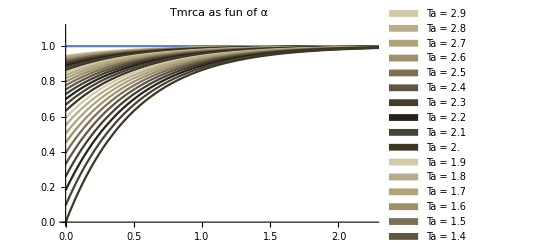

```mathematica
Module[{
T1List={0,.1,.2,.3,.4,.5,.6,.7,.8,.9,1.0,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.0,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9}, 
PlotList,
LegendItems
},
PlotList = selMeanTmrca/.{α->α,Ta->#}&/@T1List//Reverse;
LegendItems = ToString/@T1List//Reverse;
LegendItems =  "Ta = "<># &/@LegendItems;
p01 = Show[
Plot[neuMeanTmrca,{α,0,6}],
Plot[PlotList,{α,0,6},PlotRange->All,PlotStyle->ColorData[49],
PlotLegends->SwatchLegend[LegendItems]
],
PlotLabel->"Tmrca as fun of α",
PlotRange->{{0,2.25},{0,1.1}}
];
p01
]
```

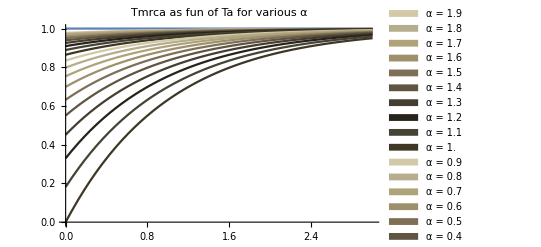

```mathematica
Module[{
alphaList={0,.1,.2,.3,.4,.5,.6,.7,.8,.9,1.0,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9}, 
PlotList,
LegendItems
},
PlotList =  selMeanTmrca/.{α->#,Ta->Ta}&/@alphaList//Reverse;
LegendItems = ToString/@alphaList//Reverse;
LegendItems =  "α = "<># &/@LegendItems;
p02 = Show[
Plot[neuMeanTmrca,{Ta,0,3}],
Plot[PlotList,{Ta,0,3},PlotRange->All,PlotStyle->ColorData[49],
PlotLegends->SwatchLegend[LegendItems]
],
PlotLabel->"Tmrca as fun of Ta for various α",
PlotRange->All
];
p02
]
```

#### distribution of time to most recent common ancestor

```mathematica
neuPDFTmrca = InverseLaplaceTransform[ tmrcaNeuGF,ω,t]
```

ⅇ^-t

```mathematica
neuCDFTmrca = InverseLaplaceTransform[tmrcaNeuGF/ω,ω,t]
```

1-ⅇ^-t

```mathematica
selPDFTmrca = InverseLaplaceTransform[tmrcaSelGFTa,ω,t]
```

ⅇ^-t+ⅇ^-Ta (-ⅇ^(-t+Ta)+DiracDelta[t-Ta]) HeavisideTheta[t-Ta] P[0,2]

```mathematica
selCDFTmrca = InverseLaplaceTransform[tmrcaSelGFTa/ω,ω,t]
```

ⅇ^-t (-1+ⅇ^t+HeavisideTheta[t-Ta] P[0,2])

```mathematica
selPDFTmrca = selPDFTmrca/.P-> PknToAlpha ;(*substituting to get as function of α for plotting*)
selCDFTmrca = selCDFTmrca/.P->PknToAlpha;
```

PDF

```mathematica
selPDFTmrca
With[{alphaList =  Table[0.25*i,{i,0,3}],TaList={0,.5,1,1.5,2}//Reverse},
LegendItems = ToString/@TaList//Reverse;
LegendItems =  "Ta = "<># &/@LegendItems;
plt[a_]:=Module[{
PlotList
},
PlotList =selPDFTmrca/.{α->a,Ta->#}&/@TaList//Reverse;
Show[
Plot[PlotList,{t,0,6},PlotRange->{{0,6},{0,1}},Exclusions->None,
(*PlotLegends->SwatchLegend[LegendItems],*)PlotLabel->"α = "<>ToString[a]
],
Plot[neuPDFTmrca/.{t->T},{t,0,6},PlotStyle->{Black,Dotted}],
PlotRange->All
]
];
rowOfPlots=plt/@alphaList;
p1 =Legended[
GraphicsRow[rowOfPlots,ImageSize->800,Spacings->0],
SwatchLegend[ColorData[97,"ColorList"],LegendItems]
];
];
p1
```

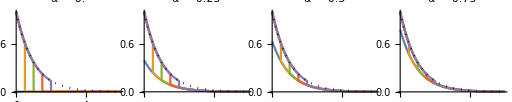

ⅇ^-t+ⅇ^(-Ta-2 α) (-ⅇ^(-t+Ta)+DiracDelta[t-Ta]) HeavisideTheta[t-Ta]

CDF

ⅇ^-t (-1+ⅇ^t+ⅇ^(-2 α) HeavisideTheta[t-Ta])

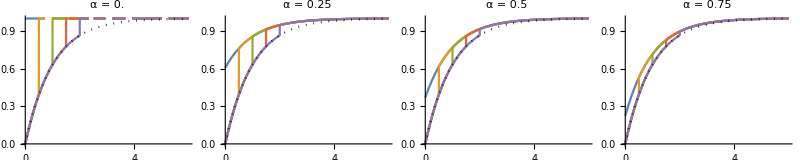

```mathematica
selCDFTmrca 
With[{alphaList =  Table[0.25*i,{i,0,3}],TaList={0,.5,1,1.5,2}//Reverse},
LegendItems = ToString/@TaList//Reverse;
LegendItems =  "Ta = "<># &/@LegendItems;
plt[a_]:=Module[{
PlotList
},
PlotList =selCDFTmrca/.{α->a,Ta->#}&/@TaList//Reverse;
Show[
Plot[PlotList,{t,0,6},PlotRange->{{0,6},{0,1}},Exclusions->None,
PlotLabel->"α = "<>ToString[a]
],
Plot[neuCDFTmrca/.{t->T},{t,0,6},PlotStyle->{Black,Dotted}],
PlotRange->All,
Exclusions->None
]
];
rowOfPlots=plt/@alphaList;
p1 =Legended[
GraphicsRow[rowOfPlots,ImageSize->800,Spacings->0],
SwatchLegend[ColorData[97,"ColorList"],LegendItems]
];
];
p1
```

Determining size of the pointmass at t = Ta:

```mathematica
lower = Limit[selCDFTmrca,{t->Ta},Direction->"FromBelow"]
upper = Limit[selCDFTmrca,{t->Ta},Direction->"FromAbove"]
pointMassSize = upper-lower//FullSimplify
```

1-ⅇ^-Ta

ⅇ^-Ta (-1+ⅇ^Ta+P[0,2])

ⅇ^-Ta P[0,2]

## n = 3 iton labeled section

Note that the MakeMeanList-type functions now require two dummy variables, which will be needed for the adaptive introgression section

```mathematica
n=3;
```

### neutral and starlike GF

```mathematica
neugfList = GFn[ω,Table[{1},{i,1,n}]]//Expand; neugfList[[0]] = List;
```

```mathematica
nmList = MakeMeanList[neugfList,n,ω,t,δ,Ta];
neuMeans = Function[{α,Ta},Evaluate[#/.P->PknToAlpha]]&/@nmList;
npList = MakePDFList[neugfList,n,ω,t,δ,Ta];
neuPdfs = Function[{α,Ta,t},Evaluate[#/.P->PknToAlpha]]&/@npList;
ncList = MakeCDFList[neugfList,n,ω,t,δ,Ta];
neuCdfs = Function[{α,Ta,t},Evaluate[#/.P->PknToAlpha]]&/@ncList;
```

```mathematica
nmList
npList//FullSimplify
ncList//FullSimplify
```

{2,1}

{6 ⅇ^-t-3/4 ⅇ^(-3 t/2) (8+3 t),1/5 ⅇ^(-3 t) (9+ⅇ^(5 t/2))}

{1-6 ⅇ^-t+ⅇ^(-3 t/2) (5+(3 t)/2),1-1/5 ⅇ^(-3 t) (3+2 ⅇ^(5 t/2))}

```mathematica
selgfDeltaList = GetGfAsList[n];
selgfTsList = InverseLaplaceTransform[1/δ #, δ, Ts]&/@selgfDeltaList;
```

```mathematica
smList = MakeMeanList[selgfDeltaList,n,ω,t,δ,Ta];
selMeans = Function[{α,Ta},Evaluate[#/.P->PknToAlpha]]&/@smList;
spList = MakePDFList[selgfDeltaList,n,ω,t,δ,Ta];
selPdfs = Function[{α,Ta,t},Evaluate[#/.P->PknToAlpha]]&/@spList;
scList = MakeCDFList[selgfDeltaList,n,ω,t,δ,Ta];
selCdfs = Function[{α,Ta,t},Evaluate[#/.P->PknToAlpha]]&/@scList;
```

PDFs for neutral case piecewise, first is singletons, second is doubletons, third is tripletons.

```mathematica
npListPieceWise =  {MakePiecewise[#,t,Ta==0],MakePiecewise[#,t,Ta>0]}&/@npList;
Print@Piecewise[Flatten[#,1]]&/@npListPieceWise
```

Piecewise[{{6 ⅇ^-t-3/4 ⅇ^(-3 t/2) (8+3 t), 0≤t<∞}, {0, True}}]

Piecewise[{{1/5 ⅇ^(-3 t) (9+ⅇ^(5 t/2)), 0≤t<∞}, {0, True}}]

{Null,Null}

PDFs for selective case, ordered by 1-Ton, 2-Ton, 3-Ton.  In each, separate the case where Ta=0 from Ta>0.

```mathematica
spListPieceWise = {MakePiecewise[#,t,Ta==0],MakePiecewise[#,t,Ta>0]}&/@spList;
Print@Piecewise[Flatten[#,1]]&/@spListPieceWise //FullSimplify
```

Piecewise[{{DiracDelta[t] P[0,3]+ⅇ^-t (P[1,3]+t (P[2,3]+P[3,3])), Ta==0&&0≤t<∞}, {ⅇ^-t t, Ta>0&&0≤t<Ta}, {1/2 ⅇ^-t (2 t+3 (1-t+Ta) P[0,2]), Ta>0&&Ta≤t<3 Ta}, {ⅇ^-t DiracDelta[t-3 Ta] P[0,3]+ⅇ^-t (P[1,3]+3 Ta (P[1,2]+P[2,2]-P[2,3]-P[3,3])+t (P[2,3]+P[3,3])), Ta>0&&3 Ta≤t<∞}, {0, True}}]

Piecewise[{{ⅇ^-t (1-P[0,3])+DiracDelta[t] P[0,3], Ta==0&&0≤t<∞}, {ⅇ^(-t-3 Ta) (ⅇ^(3 Ta)+P[0,2]+2 ⅇ^(3 t) P[0,2]-P[0,3])+ⅇ^(-3 Ta) DiracDelta[t] P[0,3], Ta>0&&0≤t<Ta}, {ⅇ^(-t-3 Ta) (-ⅇ^(3 Ta) (-1+P[0,2])+P[0,2]-P[0,3]), Ta>0&&Ta≤t<∞}, {0, True}}]

{Null,Null}

```mathematica
GetJumps[npList,ncList,t][[3]] (*note that when there are no discontinuitites, it prints nonsense back. here, only the 3-Ton branches have a discontinuitiy*)
```

{{1,{},{{{},Limit[1-6 ⅇ^-t+ⅇ^(-3 t/2) (5+(3 t)/2),MakeALim[{},t],Direction→FromAbove]-Limit[1-6 ⅇ^-t+ⅇ^(-3 t/2) (5+(3 t)/2),MakeALim[{},t],Direction→FromBelow]}}},{2,{},{{{},Limit[1-1/5 ⅇ^(-3 t) (3+2 ⅇ^(5 t/2)),MakeALim[{},t],Direction→FromAbove]-Limit[1-1/5 ⅇ^(-3 t) (3+2 ⅇ^(5 t/2)),MakeALim[{},t],Direction→FromBelow]}}}}⟦3⟧

```mathematica
Print[#]&/@GetJumps[spList,scList, t]
```

{1,{HeavisideTheta[t-3 Ta],HeavisideTheta[t-Ta],DiracDelta[t-3 Ta]},{{t-3 Ta,ⅇ^(-3 Ta) P[0,3]}}}

{2,{HeavisideTheta[t-Ta],DiracDelta[t]},{{t,ⅇ^(-3 Ta) P[0,3]}}}

{Null,Null}

## n = 4 iton labeled section

Note that the MakeMeanList-type functions now require two dummy variables, which will be needed for the adaptive introgression section

```mathematica
n=4;
```

### neutral and starlike GF

```mathematica
neugfList = GFn[ω,Table[{1},{i,1,n}]]//Expand; neugfList[[0]] = List;
```

```mathematica
nmList = MakeMeanList[neugfList,n,ω,t,δ,Ta];
neuMeans = Function[{α,Ta},Evaluate[#/.P->PknToAlpha]]&/@nmList;
npList = MakePDFList[neugfList,n,ω,t,δ,Ta];
neuPdfs = Function[{α,Ta,t},Evaluate[#/.P->PknToAlpha]]&/@npList;
ncList = MakeCDFList[neugfList,n,ω,t,δ,Ta];
neuCdfs = Function[{α,Ta,t},Evaluate[#/.P->PknToAlpha]]&/@ncList;
```

```mathematica
nmList
npList//FullSimplify 
ncList//FullSimplify
```

{2,1,2/3}

{6 ⅇ^-t-3/4 ⅇ^(-3 t/2) (8+3 t),1/5 ⅇ^(-3 t) (9+ⅇ^(5 t/2)),(2 ⅇ^-t)/3+DiracDelta[t]/3}

{1-6 ⅇ^-t+ⅇ^(-3 t/2) (5+(3 t)/2),1-1/5 ⅇ^(-3 t) (3+2 ⅇ^(5 t/2)),1-(2 ⅇ^-t)/3}

```mathematica
selgfDeltaList = GetGfAsList[n];
selgfTsList = InverseLaplaceTransform[1/δ #, δ, Ts]&/@selgfDeltaList;
```

```mathematica
smList = MakeMeanList[selgfDeltaList,n,ω,t,δ,Ta];
selMeans = Function[{α,Ta},Evaluate[#/.P->PknToAlpha]]&/@smList;
spList = MakePDFList[selgfDeltaList,n,ω,t,δ,Ta];
selPdfs = Function[{α,Ta,t},Evaluate[#/.P->PknToAlpha]]&/@spList;
scList = MakeCDFList[selgfDeltaList,n,ω,t,δ,Ta];
selCdfs = Function[{α,Ta,t},Evaluate[#/.P->PknToAlpha]]&/@scList;
```

PDFs for neutral case piecewise, first is singletons, second is doubletons, third is tripletons.

```mathematica
npListPieceWise =  {MakePiecewise[#,t,Ta==0],MakePiecewise[#,t,Ta>0]}&/@npList;
Print@Piecewise[Flatten[#,1]]&/@npListPieceWise
```

Piecewise[{{6 ⅇ^-t-3/4 ⅇ^(-3 t/2) (8+3 t), 0≤t<∞}, {0, True}}]

Piecewise[{{1/5 ⅇ^(-3 t) (9+ⅇ^(5 t/2)), 0≤t<∞}, {0, True}}]

Piecewise[{{(2 ⅇ^-t)/3+DiracDelta[t]/3, (Ta==0&&0≤t<∞)||(Ta>0&&0≤t<∞)}, {0, True}}]

{Null,Null,Null}

PDFs for selective case, ordered by 1-Ton, 2-Ton, 3-Ton.  In each, separate the case where Ta=0 from Ta>0.

```mathematica
spListPieceWise = {MakePiecewise[#,t,Ta==0],MakePiecewise[#,t,Ta>0]}&/@spList;
Print@Piecewise[Flatten[#,1]]&/@spListPieceWise
```

$Aborted

spListPieceWise

```mathematica
GetJumps[npList,ncList,t][[3]] (*note that when there are no discontinuitites, it prints nonsense back. here, only the 3-Ton branches have a discontinuitiy*)
```

Values::invrl: The argument MakeALim[{},t] is not a valid Association or a list of rules.

Limit::lim: Limit specification MakeALim[{},t] is not of the form x -> x0.

Values::invrl: The argument MakeALim[{},t] is not a valid Association or a list of rules.

Limit::lim: Limit specification MakeALim[{},t] is not of the form x -> x0.

General::stop: Further output of Limit::lim will be suppressed during this calculation.

{3,{DiracDelta[t]},{{t,1/3}}}

Here we obtain the location of the discontinuities and point masses needed in order to re-define the marginal branch length distribution functions as piece-wise continuous functions.   Below we relate these  to their context in the selective sweep model and to the main-text results about the effect of the sweep on the shape of genealogies in the surrounding genome.

```mathematica
Print[#]&/@GetJumps[spList,scList, t]
```

{1,{HeavisideTheta[t-4 Ta],HeavisideTheta[t-2 Ta],HeavisideTheta[t-Ta],DiracDelta[t-4 Ta]},{{t-4 Ta,ⅇ^(-6 Ta) P[0,4]}}}

{2,{HeavisideTheta[t-Ta],HeavisideTheta[t-2 Ta],DiracDelta[t]},{{t,ⅇ^(-6 Ta) (P[0,4]+P[1,4])}}}

{3,{DiracDelta[t],HeavisideTheta[t-Ta]},{{t,1/3 ⅇ^(-6 Ta) (ⅇ^(6 Ta)-4 P[0,3]+4 ⅇ^(3 Ta) P[0,3]+2 P[0,4]-P[1,4])}}}

{Null,Null,Null}

There are three discontinuities in the PDF of singleton branches: removable discontinuities at $t_1 = T_a$ and $t_1=2 T_a$ and a jump discontinuity at $t_1 = 4 T_a$ with a point mass of size $e^{-6 T_a} P_{0,4}$, corresponding to the case where the first event is the simultaneous coalescence of all lineages during the sweep. The PDF of $t_2$ contains two removable discontinuities, one at $t_2= T_a$ and one at $t_2 = 2 T_a$ and one point mass at $t_2 = 0$ of size $e^{-6 T_a}(P_{0,4} + P_{1,4})$. This point-mass is again caused the by multiple-merger coalescence events that give rise to a topology devoid of doubleton branches. For $t_3$, we observed a removable discontinuity at $t_3 = T_a$ and, as for the neutral case, a point-mass when $t_3 = 0$. The size of this point mass, given below, equals $P_{sym} + P_{star}$ (see above), and so is no longer a simple function of the $P_{i,k}$ under the star-like approximation, as $P_{sym}$ may result from different combinations of neutral coalescence events and sweep induced coalescence, whereas $P_{star} =P_{0,4}$ corresponds to the probability that all lineages coalesce in a sweep-induced multiple merger event:
%\begin{equation*}
%        \frac{1}{3}(1 + e^{-3T_a}4P_{0,3} - e^{-6T_a}(4 P_{0,3} + P_{1,4} - 2 P_{0,4})).
%\end{equation*}%

### Instant Yule GF

```mathematica
sample= Table[{1},{i,1,4}];
substitute[allpees_List]:=Total[δ*Peln[#[[1]],#[[2]],Total[#],s,r,Ne,M]&/@allpees]->δ;
allFs=Table[partitions[i],{i,2,Length[sample]}];
substituteL=substitute/@allFs
```

{δ Peln[0,0,2,s,r,Ne,M]+δ Peln[0,1,2,s,r,Ne,M]+δ Peln[0,2,2,s,r,Ne,M]+δ Peln[1,0,2,s,r,Ne,M]+δ Peln[1,1,2,s,r,Ne,M]+δ Peln[2,0,2,s,r,Ne,M]→δ,δ Peln[0,0,3,s,r,Ne,M]+δ Peln[0,1,3,s,r,Ne,M]+δ Peln[0,2,3,s,r,Ne,M]+δ Peln[0,3,3,s,r,Ne,M]+δ Peln[1,0,3,s,r,Ne,M]+δ Peln[1,1,3,s,r,Ne,M]+δ Peln[1,2,3,s,r,Ne,M]+δ Peln[2,0,3,s,r,Ne,M]+δ Peln[2,1,3,s,r,Ne,M]+δ Peln[3,0,3,s,r,Ne,M]→δ,δ Peln[0,0,4,s,r,Ne,M]+δ Peln[0,1,4,s,r,Ne,M]+δ Peln[0,2,4,s,r,Ne,M]+δ Peln[0,3,4,s,r,Ne,M]+δ Peln[0,4,4,s,r,Ne,M]+δ Peln[1,0,4,s,r,Ne,M]+δ Peln[1,1,4,s,r,Ne,M]+δ Peln[1,2,4,s,r,Ne,M]+δ Peln[1,3,4,s,r,Ne,M]+δ Peln[2,0,4,s,r,Ne,M]+δ Peln[2,1,4,s,r,Ne,M]+δ Peln[2,2,4,s,r,Ne,M]+δ Peln[3,0,4,s,r,Ne,M]+δ Peln[3,1,4,s,r,Ne,M]+δ Peln[4,0,4,s,r,Ne,M]→δ}

```mathematica
yulegfDeltaList = Expand @GFYule[s,r,Ne,M,ω,sample,{δ}];
yulegfDeltaList[[0]]=List;
yulegfDeltaList = yulegfDeltaList //.substituteL;
```

```mathematica
yulePDFS = MakeMargeList[yulegfDeltaList,sample,ω,δ];
yulePDFS = Total[#]&/@yulePDFS;
```

```mathematica
yuleCDFS = MakeCumuList[yulegfDeltaList,sample,ω,δ];
yuleCDFS= Total[#]&/@yuleCDFS;
```

```mathematica
#/.{s->.05,Ne->10000,r->.005,Ta->.1,M->Floor[2 * 10000*.05]}/.Peln->PELN &/@yuleCDFS(*substitution to get numerical values. then can evaluate by changing Peln to PELN*)
```

{0.+0.0774806 HeavisideTheta[-0.4+t]+0.154509 (1-ⅇ^(0.4-t)) HeavisideTheta[-0.4+t]+0.201528 (1/3-1/3 ⅇ^(-3/2 (-0.4+t))) HeavisideTheta[-0.4+t]+0.403056 (1/3-ⅇ^(0.4-t)+2/3 ⅇ^(-3/2 (-0.4+t))) HeavisideTheta[-0.4+t]+0.0330252 ⅇ^(-0.6-3/2 (-0.4+t)) (-2+2 ⅇ^(3/2 (-0.4+t))-3 (-0.4+t)) HeavisideTheta[-0.4+t]+0.132101 ⅇ^(-0.6-3/2 (-0.4+t)) (8-9 ⅇ^(1/2 (-0.4+t))+ⅇ^(3/2 (-0.4+t))+3 (-0.4+t)) HeavisideTheta[-0.4+t]+0.919853 (-(1/3+2/3 ⅇ^(0.6-(3 t)/2)-ⅇ^(0.4-t)) HeavisideTheta[-0.4+t]+1.34986 (1/3+2/3 ⅇ^(0.3-(3 t)/2)-ⅇ^(0.2-t)) HeavisideTheta[-0.2+t])+0.1996 ⅇ^(-3/2 (0.4+t)) (3 ⅇ^(0.5+t/4) (4-5 ⅇ^(t/4)+ⅇ^(5 t/4))+2 (9.11059-6 ⅇ^(0.5+t/4)+ⅇ^(3 t/2)) HeavisideTheta[-0.4+t]-6.74929 (-1.10517+ⅇ^(t/2))^2 (2.21034+ⅇ^(t/2)) HeavisideTheta[-0.2+t])+0.662891 ⅇ^(-3/2 (0.4+t)) ((1.82212-ⅇ^(3 t/2)) HeavisideTheta[-0.4+t]-1.34986 (1.34986-ⅇ^(3 t/2)) HeavisideTheta[-0.2+t])+1/30 ⅇ^(-3/2 (0.4+t)) (1.64872 (-72 ⅇ^(t/4)+90 ⅇ^(t/2)-18 ⅇ^(3 t/2)+10 ⅇ^(0.1+(3 t)/2)-5.52585 (2+3 t))+(72 ⅇ^(0.5+t/4)-2 ⅇ^(3 t/2)+9.11059 (-12.8-3 t)) HeavisideTheta[-0.4+t]-13.4986 (9 ⅇ^(0.2+t/2)-ⅇ^(3 t/2)+1.34986 (-7.4-3 t)) HeavisideTheta[-0.2+t])+0.510967 ⅇ^(-3/2 (0.4+t)) (-(-9 ⅇ^(0.4+t/2)+ⅇ^(3 t/2)+1.82212 (6.8+3 t)) HeavisideTheta[-0.4+t]-1.34986 (9 ⅇ^(0.2+t/2)-ⅇ^(3 t/2)+1.34986 (-7.4-3 t)) HeavisideTheta[-0.2+t])+0.127742 ⅇ^(-3/2 (0.4+t)) ((-2 ⅇ^(3 t/2)+1.82212 (0.8+3 t)) HeavisideTheta[-0.4+t]+1.34986 (2 ⅇ^(3 t/2)+1.34986 (-1.4-3 t)) HeavisideTheta[-0.2+t])+0.136549 ⅇ^(-2 (0.3+t)) ((-20 ⅇ^(0.6+t/2)+2 ⅇ^(2 t)+18 ⅇ^(1/3 (2.+t))) HeavisideTheta[-0.4+t]+(-30.2063+20 ⅇ^(0.6+t/2)-5 ⅇ^(0.3+2 t)) HeavisideTheta[-0.2+t]+4.94616 (6.10701+ⅇ^(2 t)-6 ⅇ^(1/3 (0.5+t))) HeavisideTheta[-0.1+t])+0.262652 ⅇ^(-2 (0.3+t)) ((40 ⅇ^(0.6+t/2)+2 ⅇ^(2 t)-15 ⅇ^(0.4+t)-27 ⅇ^(1/3 (2.+t))) HeavisideTheta[-0.4+t]+6.74929 (1.10517-ⅇ^(t/2))^3 (3.31551+ⅇ^(t/2)) HeavisideTheta[-0.2+t]+4.94616 (-6.10701+ⅇ^(2 t)-5 ⅇ^(0.1+t)+9 ⅇ^(1/3 (0.5+t))) HeavisideTheta[-0.1+t])+2/15 ⅇ^(-2 (0.3+t)) ((-ⅇ^(2 t)+81 ⅇ^(1/3 (2.+t))+5 ⅇ^(0.6+t/2) (-17.2+3 t)) HeavisideTheta[-0.4+t]+6.74929 (-13.4264+ⅇ^(2 t)+ⅇ^(0.3+t/2) (9.2-6 t)) HeavisideTheta[-0.2+t]+1.64872 (5 ⅇ^(0.1+t/2) (8-9 ⅇ^(t/2)+ⅇ^(3 t/2)+3 t)+9 (6.10701-ⅇ^(2 t)+5 ⅇ^(0.1+t)-9 ⅇ^(1/3 (0.5+t))) HeavisideTheta[-0.1+t])),0.206163+0.620551 (1/3-ⅇ^(-3 t)/3)+0.0258269 (1-ⅇ^(-t/2))+0.310276 (1/3+ⅇ^(-3 t)/15-(2 ⅇ^(-t/2))/5)+0.0374699 (2-12 ⅇ^(5 t/2)+10 ⅇ^(3 t)+3 (1.64872+4 ⅇ^(5 t/2)-5 ⅇ^(0.1+2 t)) HeavisideTheta[-0.2+t]-5 (-1.10517+ⅇ^t)^2 (1.10517+2 ⅇ^t) HeavisideTheta[-0.1+t])+0.517111 (-1+ⅇ^(3 t)+(1.34986-ⅇ^(3 t)) HeavisideTheta[-0.1+t])+0.255484 ⅇ^(-3 (0.2+t)) ((-1+ⅇ^(3 t))^2-(-1.34986+ⅇ^(3 t))^2 HeavisideTheta[-0.1+t])+0.0399067 ⅇ^(-0.6-t/2) (6-7 ⅇ^(t/2)+ⅇ^(7 t/2)+(-8.51441+7 ⅇ^(0.3+t/2)-ⅇ^(7 t/2)) HeavisideTheta[-0.1+t])+2/15 ⅇ^(-3 (0.2+t)) (-9.11059-ⅇ^(3 t)+ⅇ^(6 t)+9 ⅇ^(0.5+t)-9 ⅇ^(0.5+3 t)+5 ⅇ^(0.6+3 t)+(9.11059-ⅇ^(6 t)+5 ⅇ^(3 (0.1+t))-9 ⅇ^(0.5+t)) HeavisideTheta[-0.1+t])+0.399201 ⅇ^(-2 (0.3+t)) (-4.94616+2 ⅇ^(2 t)-2 ⅇ^(5 t)+3 ⅇ^(0.5+2 t)+(4.94616+2 ⅇ^(5 t)-5 ⅇ^(0.3+2 t)) HeavisideTheta[-0.1+t])+0.0187608 ⅇ^(-0.6-t/2) (2 (-5+7 ⅇ^(t/2)-7 ⅇ^(3 t)+5 ⅇ^(7 t/2))+7 (-3.64424+3 ⅇ^(0.5+t/2)+2 ⅇ^(3 t)-3 ⅇ^(0.1+(5 t)/2)) HeavisideTheta[-0.2+t]+(34.0576-35 ⅇ^(0.3+t/2)-10 ⅇ^(7 t/2)+21 ⅇ^(0.1+(5 t)/2)) HeavisideTheta[-0.1+t])+0.00364977 ⅇ^(-3 (0.2+t)) (-7+72 ⅇ^(5 t/2)-70 ⅇ^(3 t)+5 ⅇ^(6 t)+(12.7548-5 ⅇ^(6 t)+70 ⅇ^(3 (0.1+t))-72 ⅇ^(0.35+(5 t)/2)) HeavisideTheta[-0.1+t])+1/15 ⅇ^(-3 (0.2+t)) (1.82212-ⅇ^(3 t)+6 ⅇ^(11 t/2)-5 ⅇ^(6 t)-6 ⅇ^(0.6+(5 t)/2)+5 ⅇ^(0.6+3 t)+(-6 ⅇ^(11 t/2)+6 ⅇ^(0.6+(5 t)/2)-9 ⅇ^(0.5+3 t)+9 ⅇ^(0.1+5 t)) HeavisideTheta[-0.2+t]+(-1.82212+5 ⅇ^(6 t)+5 ⅇ^(3 (0.1+t))-9 ⅇ^(0.1+5 t)) HeavisideTheta[-0.1+t]),0.379588+0.566741 (1-ⅇ^-t)+2/15 ⅇ^(-0.6-t) (-9.11059-ⅇ^t+ⅇ^(6 t)-5 ⅇ^(3 (0.1+t))+5 ⅇ^(0.3+t)+5 ⅇ^(0.6+t)+(9.11059-ⅇ^(6 t)+5 ⅇ^(3 (0.1+t))-9 ⅇ^(0.5+t)) HeavisideTheta[-0.1+t])+0.0875505 ⅇ^(-0.6-t) (8.49859+6 ⅇ^t-ⅇ^(6 t)+5 ⅇ^(3 (0.1+t))-15 ⅇ^(0.3+t)+(-9.11059+ⅇ^(6 t)-5 ⅇ^(3 (0.1+t))+9 ⅇ^(0.5+t)) HeavisideTheta[-0.1+t])+0.0749398 (-4.74929-2 ⅇ^(5 t)+5 ⅇ^(0.3+2 t)+(4.94616+2 ⅇ^(5 t)-5 ⅇ^(0.3+2 t)) HeavisideTheta[-0.1+t])}

### i-Ton marginals: starlike vs yule approximation

```mathematica
recpersite= 1.*10^-7;
winDist = 1000;
datNe = 10000;
sweepTimes={0,.1,.25,.5,1.0,1.5,2.0}*datNe*2
classicDataShape = {10000,250,3}
```

{0,2000.,5000.,10000.,20000.,30000.,40000.}

{10000,250,3}

```mathematica
localPath = SetDirectory[NotebookDirectory[]];
pathToSims =localPath<>"/simulations/classic_marginals/";
classicSweepDataFiles = {"np_s4_0.dat",
"np_s4_0_1.dat",
"np_s4_0_25.dat",
"np_s4_0_5.dat",
"np_s4_1.dat",
"np_s4_1_5.dat",
"np_s4_2.dat"
};
classicSweepDataFiles = pathToSims<>#&/@classicSweepDataFiles
```

{/home/derek/Dropbox/projects/selection/ms_notebooks/simulations/classic_marginals/np_s4_0.dat,/home/derek/Dropbox/projects/selection/ms_notebooks/simulations/classic_marginals/np_s4_0_1.dat,/home/derek/Dropbox/projects/selection/ms_notebooks/simulations/classic_marginals/np_s4_0_25.dat,/home/derek/Dropbox/projects/selection/ms_notebooks/simulations/classic_marginals/np_s4_0_5.dat,/home/derek/Dropbox/projects/selection/ms_notebooks/simulations/classic_marginals/np_s4_1.dat,/home/derek/Dropbox/projects/selection/ms_notebooks/simulations/classic_marginals/np_s4_1_5.dat,/home/derek/Dropbox/projects/selection/ms_notebooks/simulations/classic_marginals/np_s4_2.dat}

```mathematica
classicSweepData = MapThread[MakeDataArray[#1,#2,classicDataShape,datNe]&,{sweepTimes,classicSweepDataFiles}];
```

MapThread::mptd: Object classicSweepDatFiles at position {2, 2} in MapThread[MakeDataArray[#1,#2,classicDataShape,datNe]&,{{0,2000.,5000.,10000.,20000.,30000.,40000.},classicSweepDatFiles}] has only 0 of required 1 dimensions.

The starlike approximation suffices for classic hard sweeps. We see little difference between the predictions of the starlike (dashed) and yule (solid) predictions in the figures below,  if only a slight improvement of the fit of the CDFs using the more-complicated Yule approximations.  In contrast, the computation cost increases dramatically when using the Yule approximation.

```mathematica
plt0[idxT_,idxr_,ss_,nn_]:=Block[ 
{rec = recpersite*idxr*winDist,M=Floor[2 nn 2 ss],Td=sweepTimes[[idxT]]/(2*datNe),α},
α = rec/ss Log[2 nn ss];
Show[
Plot[Evaluate[yulePDFS/.{s->ss, r->rec,Ne->nn,M->M,Ta->Td} /.Peln->PELN],{t,0,6},PlotStyle->Evaluate[Darker[#]&/@{Blue,Green,Red}],Exclusions->None,PlotRange->Full],
Plot[Evaluate[#[α,Td,t]&/@selPdfs],{t,0,6},PlotRange->Full,PlotStyle->Evaluate[{Darker[#],Dashed}&/@{Blue,Green,Red}],Exclusions->None],
Histogram[classicSweepData[[idxT]][[idxr]][[2]],{.05},"PDF",ChartStyle->Evaluate[Lighter[#]&/@{Blue,Green,Red}]
],
PlotLabel->"α= "<>ToString[α]<>"  Ta= "<>ToString[Td],
PlotRange->{{0,5},{0,2}}
]
]
```

```mathematica
plt1[idxT_,idxr_,ss_,nn_]:=Block[ 
{rec = recpersite*idxr*winDist,M=Floor[2 nn 2 ss],Td=sweepTimes[[idxT]]/(2*datNe),α},
α = rec/ss Log[2 nn ss];
Show[
Plot[Evaluate[yuleCDFS/.{s->ss, r->rec,Ne->nn,M->M,Ta->Td} /.Peln->PELN],{t,0,6},PlotStyle->Evaluate[Darker[#]&/@{Blue,Green,Red}],Exclusions->None,PlotRange->Full],
Plot[Evaluate[#[α,Td,t]&/@selCdfs],{t,0,6},PlotRange->Full,PlotStyle->Evaluate[{Darker[#],Dashed}&/@{Blue,Green,Red}],Exclusions->None],
Histogram[classicSweepData[[idxT]][[idxr]][[2]],{.05},"CDF",ChartStyle->Evaluate[Lighter[#]&/@{Blue,Green,Red}]
],
PlotLabel->"α= "<>ToString[α]<>"  Ta= "<>ToString[Td],
PlotRange->{{0,5},{0,1.01}}
]
]
```

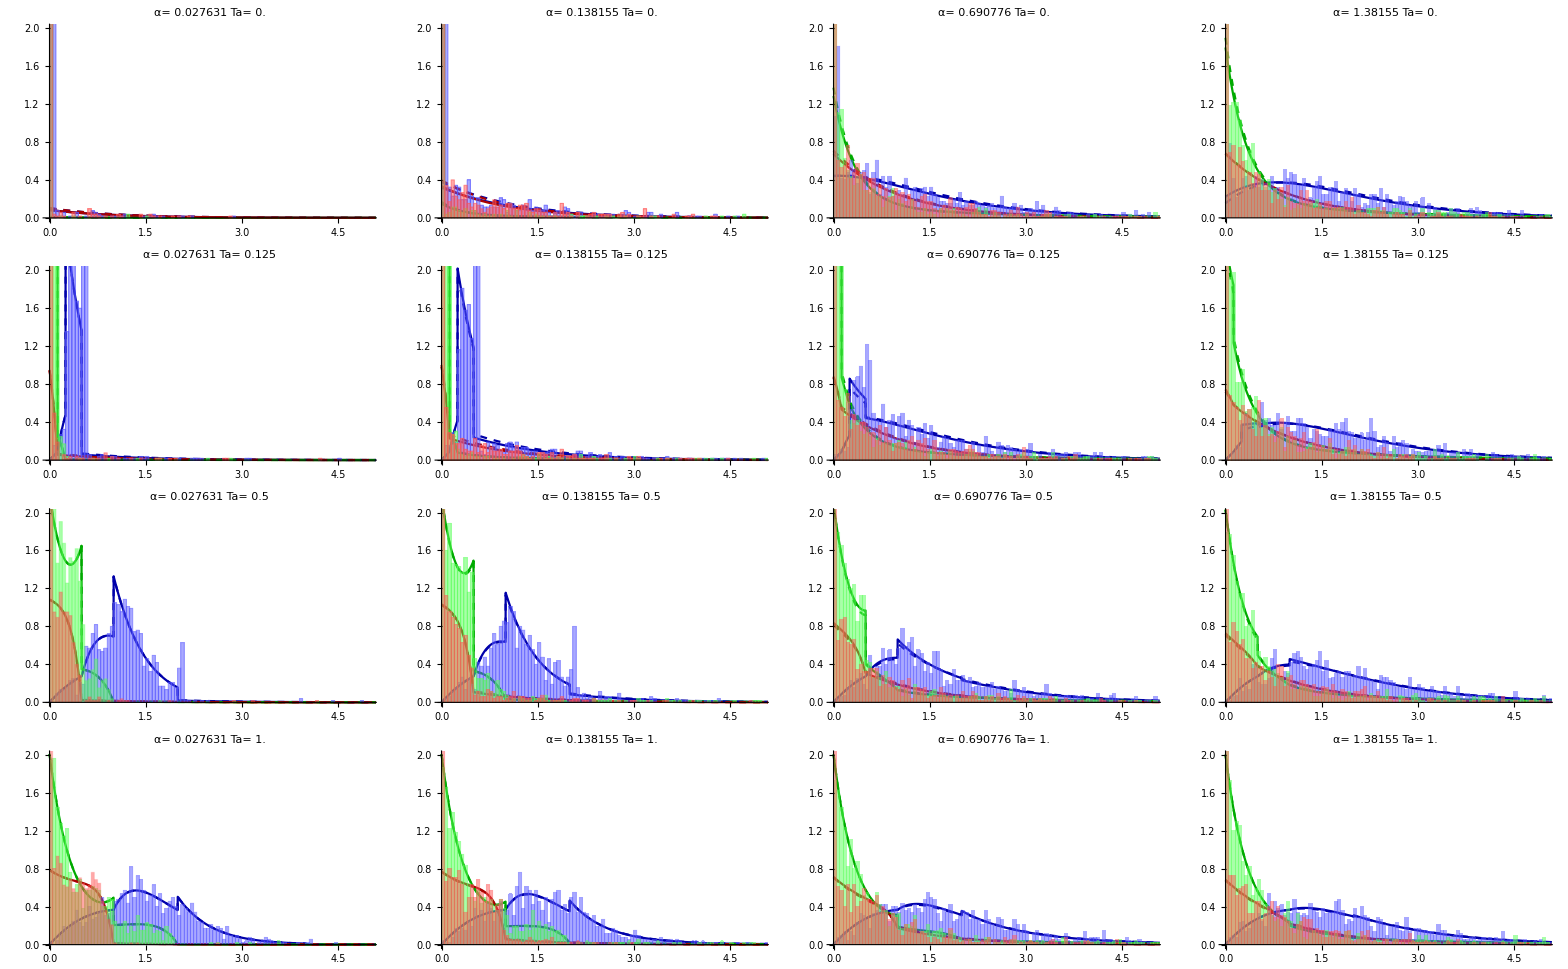

```mathematica
GraphicsGrid[
Table[
Table[ 
plt0[idxT,idxr,.05,10000],{idxr,{2,10,50,100}}],{idxT,{1,3,5,7}}],
ImageSize->Full,Spacings->0
]
```

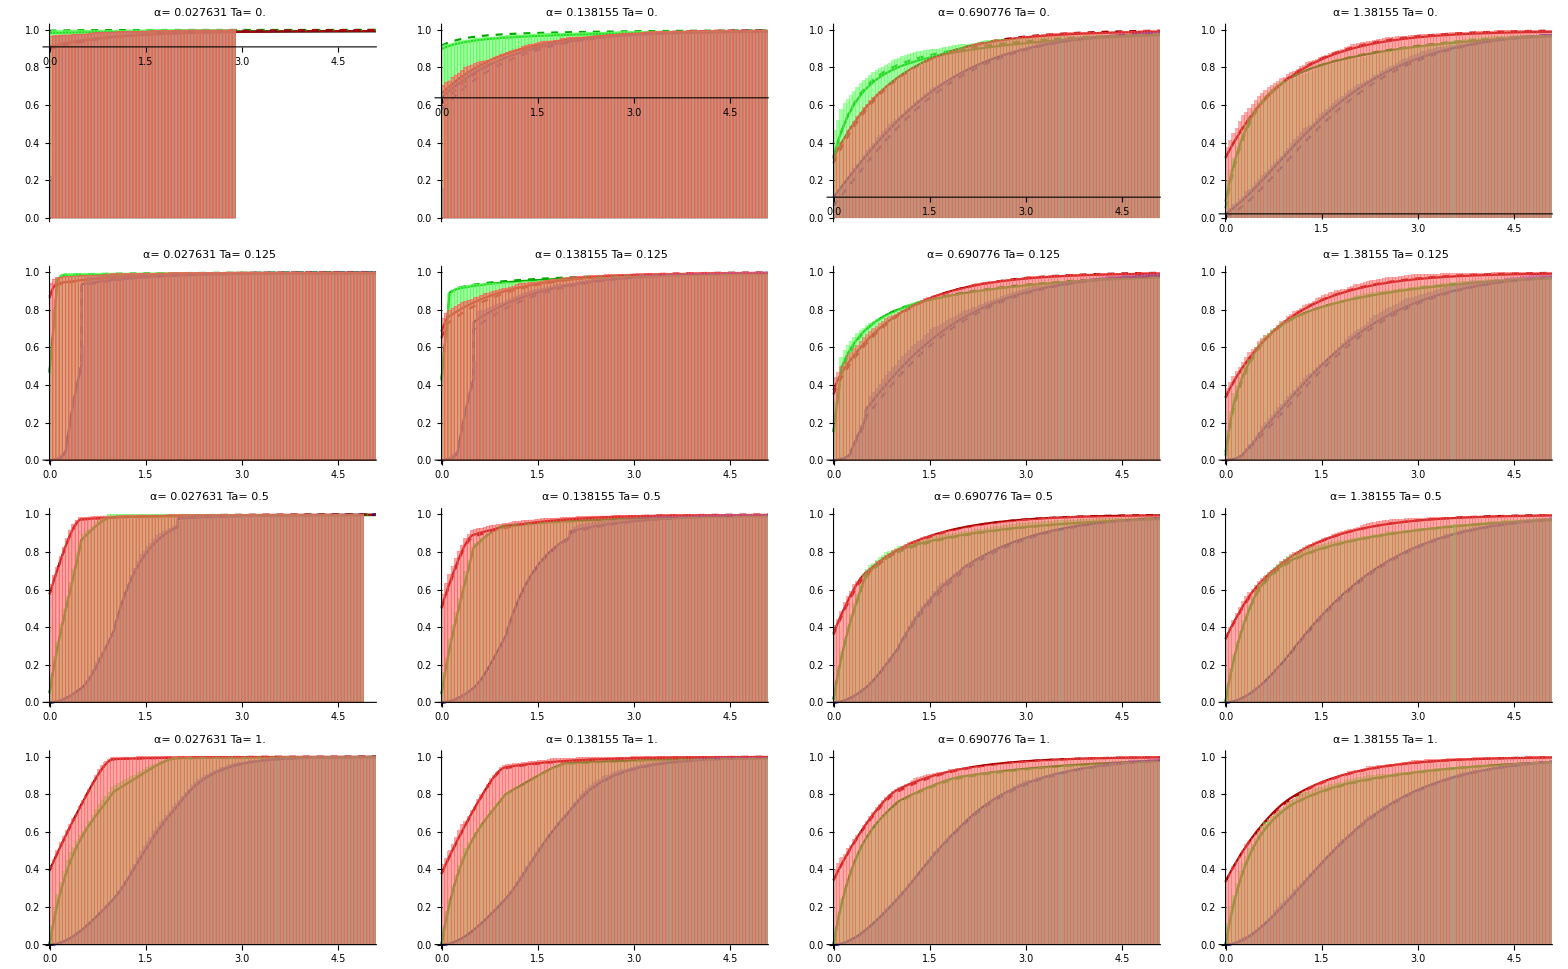

```mathematica
GraphicsGrid[
Table[
Table[ 
plt1[idxT,idxr,.05,10000],{idxr,{2,10,50,100}}],{idxT,{1,3,5,7}}],
ImageSize->Full,Spacings->0
]
```

## Site Frequency Spectrum, n = 9

```mathematica
(*n=9;
gfList = Block[{sample = Table[{1},{i,1,n}],gfDeltaEpsilon},
gfDeltaEpsilon =GFstar[α,ω,sample,δ] //Expand;
gfDeltaEpsilon[[0]] = List;
gfDeltaEpsilon = SubSimplifyPeeRulesv2[#,n]&/@gfDeltaEpsilon//Parallelize;
gfDeltaEpsilon];

meansList = MakeMeanList[gfList,n,ω,t,δ,Ta];
DumpSave["iTonBL_9_gfList_meanList.mx",{gfStarList,meansList}]*)
```

```mathematica
SetDirectory[NotebookDirectory[]];
(*DumpSave["iTonBL_9_gfList_meanList.mx",{gfStarList,meansList}]*)
Get["iTonBL_9_gfList_meanList.mx"];
meanItonFunList = Function[{α,Ta},Evaluate[#//.P->PknToAlpha]]&/@meanList;
sfs[α_,Ta_]:=Block[{a = #[α,Ta]&/@meanItonFunList},a/Total[a]]
```

```mathematica
talist = {0.00000001,.1,.25,.5,1,1.5,2};
alphaList = {0,0.25,0.5};
legendItems = "Ta= "<>ToString[#]&/@{0,.1,.25,.5,1,1.5,2};
titleItems = "α= "<>ToString[#]&/@{0,.25,.75}

(*plt1 = getSFS[expectedBLs,0,#]&/@tslist;
plt2 = getSFS[expectedBLs,0.25,#]&/@tslist;
plt3 = getSFS[expectedBLs,0.75,#]&/@tslist;*)
plt1 = sfs[0,#]&/@talist;
plt2 = sfs[0.25,#]&/@talist;
plt3 = sfs[0.75,#]&/@talist;
```

{α= 0,α= 0.25,α= 0.75}

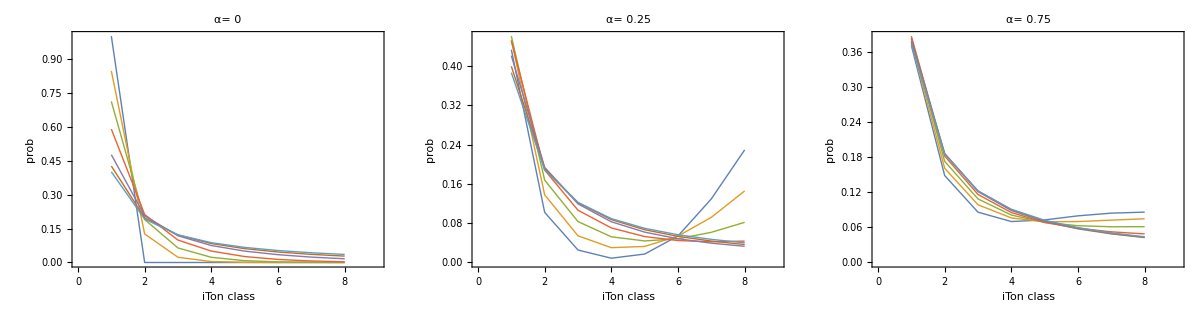

```mathematica
pltFull = GraphicsRow[
MapThread[ 
ListPlot[#1,Joined->True,PlotRange->{{0,9},All},Frame->{{True,False},{True,False}},FrameLabel->{"iTon class","prob"},FrameStyle->Directive[Thick,Black,Bold,12],LabelStyle->Directive[12,Bold,Black],PlotStyle->Directive[12,Bold,Thick],
(*PlotLegends->SwatchLegend[legendItems],*)
PlotLabel->#2]&,{{plt1,plt2,plt3},titleItems}
],
Spacings->0,ImageSize->Full
];
(*Export["~/Dropbox/projects/selection/figs_for_ms/n=9_sfs.pdf",pltFull];*)
pltFull
```